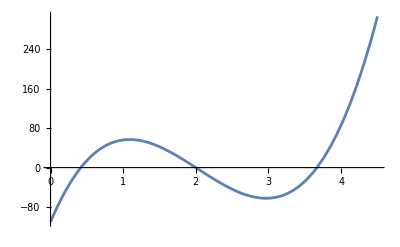

```mathematica
f[x_]:=36 x^3-219 x^2+349 x-110
Plot[f[x],{x,0,4.5}]
```

```mathematica
secantMethod[f_,a_,b_,eps_]:=Module[{x0=a,x1=b,x2,iter=0,history={}},While[True,x2=x1-f[x1]*(x1-x0)/(f[x1]-f[x0]);
iter++;
AppendTo[history,{iter,N[x2,6],N[f[x2],6],N[Abs[x2-x1],6]}];
If[Abs[x2-x1]<eps,Break[]];
x0=x1;
x1=x2;];
{N[x2,6],iter,history}]
```

```mathematica
result=secantMethod[f,3.0,4.0,10^-3];
```

Set::setraw: Cannot assign to raw object 3..

Set::setraw: Cannot assign to raw object 4..

Set::setraw: Cannot assign to raw object 3..

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
Print["Найденный корень: ",result[[1]]];
Print["Потребовавшееся число итераций: ",result[[2]]];
Print["Таблица итераций:"];
Print[TableForm[result[[3]]]]
```

Найденный корень: f

Потребовавшееся число итераций: 3.

Таблица итераций:

4.